## resonant excitation - Rabi frequency calculation

```mathematica
ns=10^-9;
μm=10^-6;
MHz=10^6;
e=1.60217663*^-19;
a0=5.29177210903*^-11;
ℏ=(6.626*^-34)/(2π);
c=2.998*^8;
ϵ0=8.85*^-12;
i=3/2;
(*E1MatElemHF[{F_,mF_,J_},{FF_,mFF_,JJ_},q_]:=(-1)^(FF+J+1+i)√(2FF+1)SixJSymbol[{J,JJ,1},{FF,F,i}]ClebschGordan[{F,mF},{1,q},{FF,mFF}];*)
(*E1MatElemHF[{F_,mF_,J_},{FF_,mFF_,JJ_},q_]:=(-1)^(FF+J+1+i)(-1)^(FF-1+mF)√((2FF+1)(2J+1)(2F+1))SixJSymbol[{J,JJ,1},{FF,F,i}]ThreeJSymbol[{FF,mFF},{1,-q},{F,-mF}];(*correct, based on Steck*)*)
E1MatElemHF[{F_,mF_,J_},{FF_,mFF_,JJ_},q_]:=(-1)^(FF+J+1+i)√((2FF+1)(2J+1))SixJSymbol[{J,JJ,1},{FF,F,i}]ClebschGordan[{FF,mFF},{1,-q},{F,mF}];
```

```mathematica
J=1/2;JJ=3/2;FF=0;F=1;i=3/2;
SixJSymbol[{J,JJ,1},{FF,F,i}]
SixJSymbol[{JJ,i,FF},{F,1,J}]
```

-1/(2 √3)

-1/(2 √3)

```mathematica
"d"
d=4.227e a0 E1MatElemHF[{1,0,1/2},{0,0,3/2},0]
τ=20ns;
w0=300μm;(*beam waist*)
```

d

1.46308×10^-29

Check with Steck’s result for stretched state transition on 2-3’

```mathematica
(4.227 e a0 E1MatElemHF[{2,2,1/2},{3,3,3/2},1])/(2.5343*10^-29)
```

0.999933

Square pulse excitation

```mathematica
P=((ℏ π)/(d τ))^2(c ϵ0 π w0^2)/4;(*this the power need for Ωτ=π if we excite with a square pulse*)
"Power (μW)"
P 10^6
```

Power (μW)

240.411

Gaussian pulse excitation

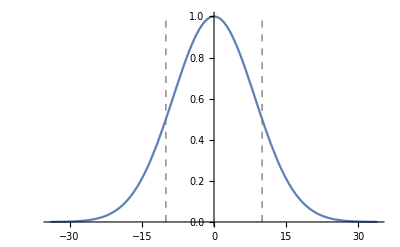

```mathematica
tFWHM =20ns;
τ=0.5tFWHM/√(2 Log[2]);
Plot[Exp[-(t ns)^2/(2 τ^2)],{t,-4τ/ns,4τ/ns},PlotRange->All,FrameLabel->{"Pulse amplitude (arb.)","ns"}, Epilog->{Directive[Gray,Dashed],Line[{{-0.5tFWHM/ns,0},{-0.5tFWHM/ns,1}}],Line[{{0.5tFWHM/ns,0},{0.5tFWHM/ns,1}}]}]
```

By computing Integral(Ω(t)dt) = π, we can work out the peak Rabi frequency needed, and subsequently the peak power needed. This is given by (see note in Overleaf or Obsidian in “my quantum network”)

```mathematica
d=4.227e a0 E1MatElemHF[{1,0,1/2},{0,0,3/2},0];
w0=300μm;(*beam waist*)
tFWHM =20ns;
P0=ℏ^2/d^2(π^2 w0^2 Log[2]c ϵ0)/tFWHM^2
```

0.000212173

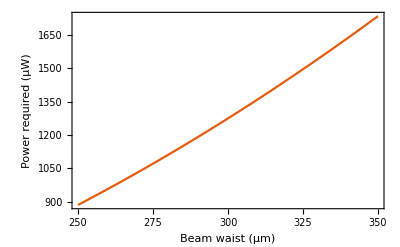

```mathematica
Plot[ℏ^2/d^2(π^2(w*10^-6)^2 Log[2]c ϵ0)/tFWHM^2 10^6,{w,250,350},PlotTheme->"Scientific",FrameLabel->{"Beam waist (μm)","Power required (μW)"}]
```

## off-resonant scattering

How much of a concern is scattering from the F’=2 when we excite resonantly F=1->F’=0?  ignore coupling to states other than m=0.

```mathematica
ns=10^-9;
μm=10^-6;
MHz=10^6;
e=1.6*^-19;
a0=5*^-11;
ℏ=(6.602*^-34)/(2π);
c=2.998*^8;
ϵ0=8.85*^-12;
i=3/2;
```

```mathematica
"d"
```

```mathematica
d=4.227e a0 E1MatElemHF[{1,0,1/2},{0,0,3/2},0]
γ=2π*6.066*^6;
Isat=(ϵ0 c ℏ^2 γ^2)/(4 d^2);(*Mark's notes*)
τ=30ns;
w0=300μm;(*beam waist*)
P=((ℏ π)/(d τ))^2(c ϵ0 π w0^2)/4;(*this the power need for Ωτ=π if we excite with a square pulse*)
"Power (μW)"
P 10^6
```

-5.636×10^-30

Power (μW)

714.848

```mathematica
E1MatElemHF[{F_,mF_,J_},{FF_,mFF_,JJ_},q_]:=(-1)^(FF+J+1+i)√(2FF+1)SixJSymbol[{J,JJ,1},{FF,F,i}]ClebschGordan[{F,mF},{1,q},{FF,mFF}];
"1,0 to 0',0"
E1MatElemHF[{1,0,1/2},{0,0,3/2},0]
"1,0 to 1',0"
E1MatElemHF[{1,0,1/2},{1,0,3/2},0]
"1,0 to 2',0"
E1MatElemHF[{1,0,1/2},{2,0,3/2},0]
```

1,0 to 0',0

-1/6

1,0 to 1',0

0

1,0 to 2',0

(√5)/6

```mathematica
ClebschGordan[{1,0},{1,0},{1,0}]
```

```mathematica
4.227e a0 E1MatElemHF[{1,0,1/2},{2,0,3/2},0]
```

1.26025×10^-29

Gaussian pulse:

```mathematica
1/(2π)1/(30ns)//N
```

5.30516×10^6

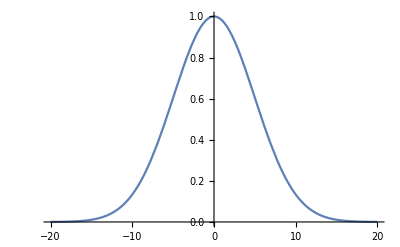

```mathematica
tFWHM =30ns;
τ=0.5tFWHM/√(2 Log[2]);
Plot[Exp[-π^2 2π (f 10^6)^2 2 τ^2],{f,-20,20},PlotRange->All,FrameLabel->{"Pulse amplitude (arb.)","MHz"}]
```

So the pulse width is ~ 10 MHz, F’=0 and F’=2 are separated by ~ 250 MHz, and the linewidth of F’=1 is ~ 6 MHz. However, the amount of coupling we get also depends on the Rabi frequency of the light. We are ultimately interested in how much scattering we get from the F’=2, m=0 state over the duration of exciting F’=0. We can approximate F=0 to F’=1 as a two-level system and ingore coherence since the population transfer itself is expected to be very small.

For a Gaussian pulse envelope, we need to first more carefully calculate what the peak Rabi frequency needs to be. By computing Integral(Ω(t)dt) = π, we can work out the peak Rabi frequency needed, and subsequently the peak power needed. This is given by (see note in Overleaf or Obsidian in “my quantum network”)

```mathematica
d=4.227e a0 E1MatElemHF[{1,0,1/2},{0,0,3/2},0];
w0=300μm;(*beam waist*)
tFWHM =20ns;
P0=ℏ^2/d^2(π^2 w0^2 Log[2]c ϵ0)/tFWHM^2
```

0.00141949

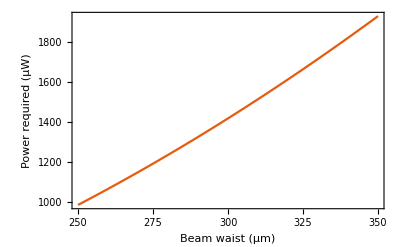

```mathematica
Plot[ℏ^2/d^2(π^2(w*10^-6)^2 Log[2]c ϵ0)/tFWHM^2 10^6,{w,250,350},PlotTheme->"Scientific",FrameLabel->{"Beam waist (μm)","Power required (μW)"}]
```

```mathematica
d
```

-5.636×10^-30

```mathematica
Plot[Exp[-t^2/(2 τ^2)],{t,-3τ,3τ}]
```

```mathematica
Exp[-t^2/(2 τ^2)]/.t->τ √(2 Log[2])
```

0.5

```mathematica
Log[ⅇ]
```

1

## misc testing

Checking relation between 3J and Clebsch-Gordon as defined in Mathematica

```mathematica
F=2;mF=2;FF=3;mFF=3;
q=1;
ClebschGordan[{F,mF},{1,q},{FF,mFF}]
(-1)^(F-1+mFF)√(2FF+1)ThreeJSymbol[{F,mF},{1,q},{FF,-mFF}]
```

1

1

```mathematica
Clear[F,mF,FF,mFF,q];
ClebschGordan[{F,mF},{1,q},{FF,mFF}]
```

(-1)^(-1+F+mFF) √(1+2 FF) ThreeJSymbol[{F,mF},{1,q},{FF,-mFF}]

```mathematica
Clear[F,mF,FF,mFF,q,J,JJ,i]
```

```mathematica
(*this matrix element is correct, judged by comparing to Steck's matrix elemnt for the D2 stretched state transition on F=2 to F=3*)
(-1)^(FF+J+1+i)(-1)^(FF-1+mF)√((2FF+1)(2J+1)(2F+1))SixJSymbol[{J,JJ,1},{FF,F,i}]ThreeJSymbol[{FF,mFF},{1,-q},{F,-mF}]
```

(-1)^(2 FF+i+J+mF) √((1+2 F) (1+2 FF) (1+2 J)) SixJSymbol[{J,JJ,1},{FF,F,i}] ThreeJSymbol[{FF,mFF},{1,-q},{F,-mF}]

Reformulate this matrix element in terms of the Clebsch Gordon coefficient, which I prefer to the 3J:

```mathematica
ThreeJSymbol[{FF,mFF},{1,-q},{F,-mF}]
ClebschGordan[{FF,mFF},{1,q},{F,mF}]
```

ThreeJSymbol[{FF,mFF},{1,-q},{F,-mF}]

(-1)^(-1+FF+mF) √(1+2 F) ThreeJSymbol[{FF,mFF},{1,q},{F,-mF}]

```mathematica
(-1)^(FF+J+1+i)√((2FF+1)(2J+1))SixJSymbol[{J,JJ,1},{FF,F,i}]ClebschGordan[{FF,mFF},{1,-q},{F,mF}]
```

(-1)^(2 FF+i+J+mF) √(1+2 F) √((1+2 FF) (1+2 J)) SixJSymbol[{J,JJ,1},{FF,F,i}] ThreeJSymbol[{FF,mFF},{1,-q},{F,-mF}]

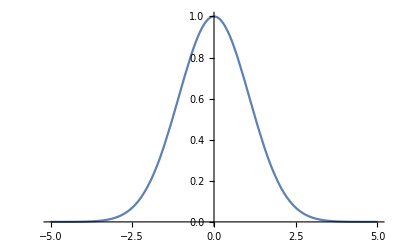

```mathematica
τ=30ns;(*Gaussian pulse FWHM*)
σ=τ/(4 Log[2]);
A=1;
f[t_]:=A ⅇ^(-t^2/(2 σ^2));
Plot[Abs[f[t]],{t,-50ns,50ns}]
```

```mathematica
F[Δ_]=1/(2π)Integrate[ⅇ^(ⅈ Δ t)f[t],{t,-∞,∞}]
```

(3 ⅇ^(-(9 Δ^2)/(320000000000000000 Log[2]^2)))/(400000000 √(2 π) Log[2])

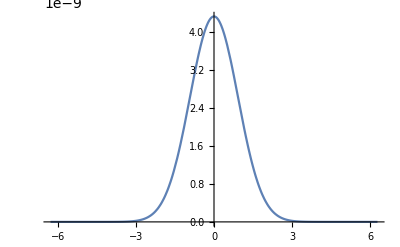

```mathematica
Plot[F[Δ],{Δ,-2π 100MHz,2π 100MHz}]
```

```mathematica
Integrate[s/(1+4(Δ/γ)^2+s)]
```

Plot[f[Δ],{Δ,-10 MHz,10 MHz}]

Integral[(s γ)/(1+s+(4 Δ^2)/γ^2)]

```mathematica
Refine[Abs[Integrate[ⅇ^(-ⅈ 2π Δ t),{t,0,τ}]]^2//FullSimplify,Δ∈Reals]
```

(Abs[(1-ⅇ^(-2 ⅈ π Δ τ))/Δ]^2)/(4 π^2)

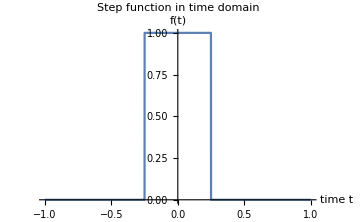

```mathematica
f[t_]:=Piecewise[{{1,t>-a τ/2 && t<a τ/2},{0,t>a τ/2 && t < a τ/2}}]
τ=1;
 a=.5;
Plot[f[t],{t,-τ,τ},PlotLabel->Style["Step function in time domain",Black,Medium],AxesLabel->{"time t","f(t)"},LabelStyle->Directive[Black],ImageSize->Medium]
```

```mathematica
Clear[a,τ]
F[ω_]=FourierTransform[f[t],t,ω]
τ=30*^-9;
 a=1;
F[ω_]=FourierTransform[f[t],t,ω]
```

-1/ω √(2/π) Sin[(a τ ω)/2] (-1+UnitStep[-a] (-1+UnitStep[-τ]) (UnitStep[a] (-1+UnitStep[τ])-UnitStep[τ])-UnitStep[a] UnitStep[-τ] (-1+UnitStep[τ])+UnitStep[-τ] UnitStep[τ])

(√(2/π) Sin[(3 ω)/200000000])/ω

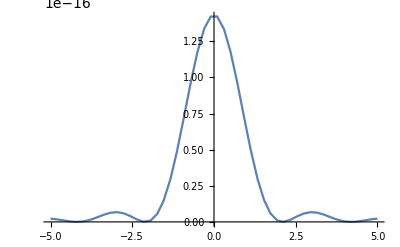

```mathematica
Plot[F[ω]^2,{ω,-0.5*10^9,0.5*10^9},PlotRange->All]
```

The excitation pulse is ~ 200 rad/s =  30 MHz broad